```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
ys =FullSimplify[ Solve[im==0,y]];
```

```mathematica
xs = Solve[im==0,x];
```

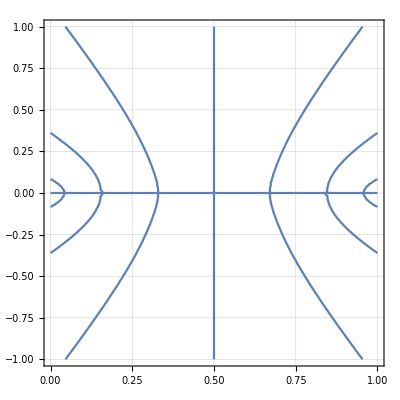

```mathematica
imμ =im/.μ-> 3.8284;
ContourPlot[imμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic]
```

(0.-0.36139 ⅈ) √(-1-7.6568 (-1+x0) x0)

(0.+0.36139 ⅈ) √(-1-7.6568 (-1+x0) x0)

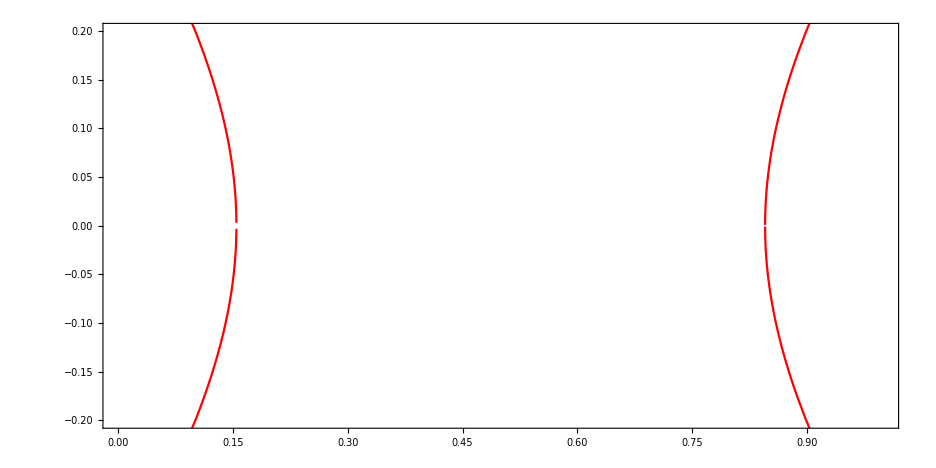

```mathematica
ys11 = ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}
ys12 = ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0}
Show[Show[ParametricPlot[{x0+ ϵlist11⟦2,1,2⟧, ys11},{x0,0.8,1},PlotRange->{{0,1},{-0.2,0.2}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist11⟦2,1,2⟧, ys11},{x0,0.8,1},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ ϵlist11⟦1,1,2⟧, ys11},{x0,0,0.2},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist11⟦1,1,2⟧, ys11},{x0,0,0.2},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2],Show[ParametricPlot[{x0+ ϵlist12⟦2,1,2⟧, ys12},{x0,0.8,1},PlotRange->{{0,1},Automatic},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist12⟦2,1,2⟧, ys12},{x0,0.8,1},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ ϵlist12⟦1,1,2⟧, ys12},{x0,0,0.2},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist12⟦1,1,2⟧, ys12},{x0,0,0.2},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
Plot[ys⟦3,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2]]
```

```mathematica
ys11 = ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}
ys12 = ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0}
Show[Show[ParametricPlot[{x0+ ϵlist11⟦2,1,2⟧, ys11},{x0,0.8,1},PlotRange->{{0,1},{-0.2,0.2}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist11⟦2,1,2⟧, ys11},{x0,0.8,1},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ ϵlist11⟦1,1,2⟧, ys11},{x0,0,0.2},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist11⟦1,1,2⟧, ys11},{x0,0,0.2},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2],Show[ParametricPlot[{x0+ ϵlist12⟦2,1,2⟧, ys12},{x0,0.8,1},PlotRange->{{0,1},Automatic},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist12⟦2,1,2⟧, ys12},{x0,0.8,1},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ ϵlist12⟦1,1,2⟧, ys12},{x0,0,0.2},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist12⟦1,1,2⟧, ys12},{x0,0,0.2},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
Plot[ys⟦3,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2]]
```

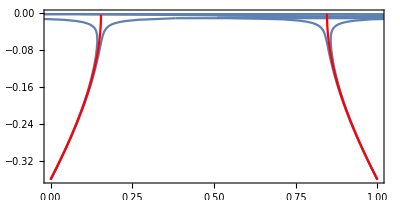

```mathematica
Show[ParametricPlot[{x0+ ϵlist12⟦2,1,2⟧, ys12},{x0,0.8,1},PlotRange->{{0,1},Automatic},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist12⟦2,1,2⟧, ys12},{x0,0.8,1},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ ϵlist12⟦1,1,2⟧, ys12},{x0,0,0.2},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist12⟦1,1,2⟧, ys12},{x0,0,0.2},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
Plot[ys⟦3,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2]
```

```mathematica
bandaseries
```

(214.817 (1-2 x0)^2 √(-1-7.6568 (-1+x0) x0) (-2+3.8284 (1+7.6568 x0 (-1+2 x0)) (1+3.8284 (2-6 x0+4 x0^2))) ϵ)/(√(-1-7.6568 (-1+x0+ϵ) (x0+ϵ)))

```mathematica
ys21 = ys⟦4,1,2⟧/.{μ-> 3.8284,x-> x0}
```

-(√(1.26121+6 (-1+x0) x0-0.133498 √(1.8284+29.3133 (1-2 x0)^2+56.1115 (1-2 x0)^2 (1+8 (-1+x0) x0))))/(√2)

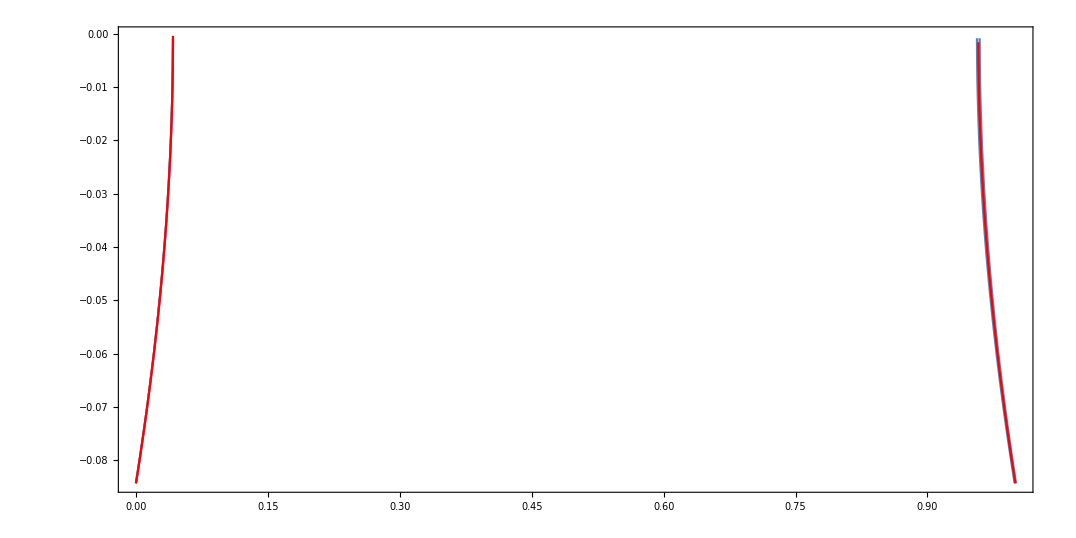

```mathematica
Show[ParametricPlot[{x0+ ϵteste⟦2,1,2⟧, ys21},{x0,0.8,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵteste⟦2,1,2⟧, ys21},{x0,0.8,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+ ϵteste⟦1,1,2⟧, ys21},{x0,0,0.2},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵteste⟦1,1,2⟧, ys21},{x0,0,0.2},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦4,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2]
```

```mathematica
r11 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦2,1,2⟧/.{y-> ys⟦2,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r12 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦3,1,2⟧/.{y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r21 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦4,1,2⟧/.{y-> ys⟦4,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r22 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦5,1,2⟧/.{y-> ys⟦5,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r31 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦6,1,2⟧/.{y-> ys⟦6,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r32 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦7,1,2⟧/.{y-> ys⟦7,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
rlist={};
Table[AppendTo[rlist, FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦i,1,2⟧/.{y-> ys⟦i,1,2⟧}/.x-> x0 ]/.μ-> 3.8284],{i,2,7,1}];
```

```mathematica
Length[rlist]
```

6

```mathematica
Length[ϵlist]
```

6

```mathematica
ϵlist = {};
Table[AppendTo[ϵlist, Reduce[Abs[rlist⟦i⟧]== 1,ϵ,Reals]],{i,1,6,1}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

```mathematica
ϵlist⟦6⟧;
```

```mathematica
ϵ11 = Reduce[Abs[r11]== 1,ϵ,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

(x0<0.185707&&(ϵ==-(1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6))||ϵ==1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)))||(0.185707<x0<0.356413&&(ϵ==1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)||ϵ==-(1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6))))||(0.356413<x0<0.5&&(ϵ==-(1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6))||ϵ==1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)))||(0.5<x0<0.643587&&(ϵ==-(1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6))||ϵ==1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)))||(0.643587<x0<0.814293&&(ϵ==1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)||ϵ==-(1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6))))||(x0>0.814293&&(ϵ==-(1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6))||ϵ==1.84673×10^16/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)))

```mathematica
ϵ12= Reduce[Abs[r12]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ21= Reduce[Abs[r22]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ22= Reduce[Abs[r22]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ31= Reduce[Abs[r31]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ32= Reduce[Abs[r32]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
part11A = ϵ11⟦1,2,1,2⟧;
part11B= ϵ11⟦1,2,2,2⟧;
ys11 = ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0};
```

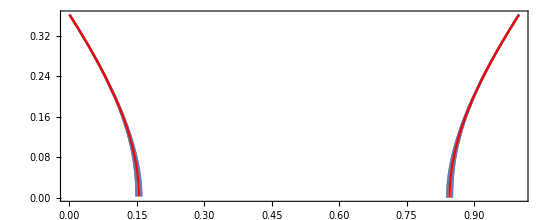

```mathematica
Show[ParametricPlot[{x0+part11A, ys11},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part11A, ys11},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part11B, ys11},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part11B, ys11},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red]]
```

```mathematica
Length[ϵ32]
```

14

```mathematica
part11A = ϵ11⟦1,2,1,2⟧;
part11B= ϵ11⟦1,2,2,2⟧;
ys11 = ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0};

part12A = ϵ12⟦1,2,1,2⟧;
part12B= ϵ12⟦1,2,2,2⟧;
ys12 = ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0};

part21A = ϵ21⟦1,2,1,2⟧;
part21B= ϵ21⟦1,2,2,2⟧;
ys21 = ys⟦4,1,2⟧/.{μ-> 3.8284,x-> x0};

part22A = ϵ21⟦1,2,1,2⟧;
part22B= ϵ21⟦1,2,2,2⟧;
ys22 = ys⟦5,1,2⟧/.{μ-> 3.8284,x-> x0};

part31A = ϵ31⟦1,2,1,2⟧;
part31B= ϵ31⟦1,2,2,2⟧;
ys31= ys⟦6,1,2⟧/.{μ-> 3.8284,x-> x0};

part32A = ϵ32⟦1,2,1,2⟧;
part32B= ϵ32⟦1,2,2,2⟧;
ys32 = ys⟦7,1,2⟧/.{μ-> 3.8284,x-> x0};
```

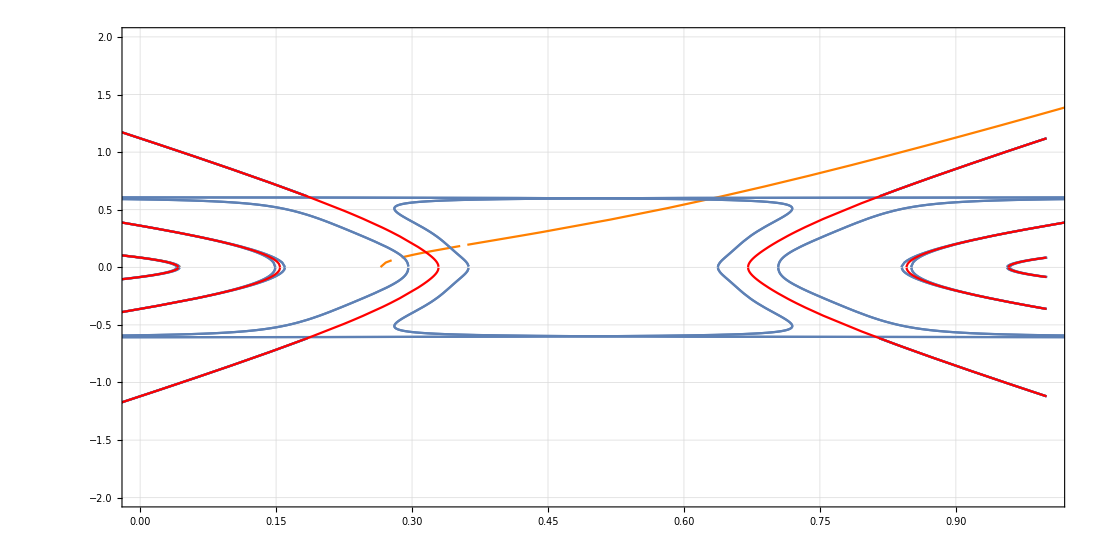

```mathematica
Show[ParametricPlot[{x0+part11A, ys11},{x0,-2,2},PlotRange->{{0,1},{-2,2}},Frame->True,MaxRecursion->5,GridLines->Automatic],
ParametricPlot[{x0-  part11A, ys11},{x0,-2,2},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part11B, ys11},{x0,-2,2},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part11B, ys11},{x0,-2,2},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,-2,2},PlotStyle->Red],


ParametricPlot[{x0+ϵ111, ys11},{x0,-2,2},PlotRange->{{-2,2},All},Frame->True,MaxRecursion->5,GridLines->Automatic, PlotStyle->Orange],
ParametricPlot[{x0-  ϵ111, ys11},{x0,-2,2},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5, PlotStyle->Orange],
ParametricPlot[{x0+part111B, ys11},{x0,-2,2},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5, PlotStyle->Orange],
ParametricPlot[{x0-  part111B, ys11},{x0,-2,2},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5, PlotStyle->Orange],



ParametricPlot[{x0+part12A, ys12},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part12A, ys12},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part12B, ys12},{x0,-1,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part12B, ys12},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦3,1,2⟧/.μ-> 3.8284,{x,-1,1},PlotStyle->Red],

ParametricPlot[{x0+part21A, ys21},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part21A, ys21},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part21B, ys21},{x0,-1,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part21B, ys21},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦4,1,2⟧/.μ-> 3.8284,{x,-1,1},PlotStyle->Red],

ParametricPlot[{x0+part22A, ys22},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part22A, ys22},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part22B, ys22},{x0,-1,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part22B, ys22},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦5,1,2⟧/.μ-> 3.8284,{x,-1,1},PlotStyle->Red],

ParametricPlot[{x0+part31A, ys31},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part31A, ys31},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part31B, ys31},{x0,-1,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part31B, ys31},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦6,1,2⟧/.μ-> 3.8284,{x,-1,1},PlotStyle->Red],

ParametricPlot[{x0+part32A, ys32},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part32A, ys32},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part32B, ys32},{x0,-1,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part32B, ys32},{x0,-1,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦7,1,2⟧/.μ-> 3.8284,{x,-1,1},PlotStyle->Red],
AspectRatio-> 1/2]
```

```mathematica
r111 = FullSimplify[(im/.x-> x0+ϵ)/ys⟦2,1,2⟧/.{y-> ys⟦2,1,2⟧}/.x-> x0 ]/.μ-> 3.8284
```

214.817 ϵ (-1+2 x0+ϵ) (-1+2 x0+2 ϵ) (1.8284+29.3133 (-1+2 x0+2 ϵ)^2+224.446 (4 x0^4+x0^2 (5-12 ϵ)+8 x0^3 (-1+ϵ)-(-1+ϵ)^2 ϵ^2+x0 (-1+4 ϵ-4 ϵ^3)))

```mathematica
ϵ111 = Reduce[Abs[r111]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
part111A = ϵ111;
part111B= ϵ111⟦1,2,2,2⟧;
ys11 = ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0};
```

Part::partd: Part specification ϵ111⟦1,2,2,2⟧ is longer than depth of object.

O resultado obtido para as bandas 1 e 2 coincidiram perfeitamente com o comportamento esperado (bandas de atração no formato de banana). 
Entretanto, para a banda 3 observamos um comportamento que foge à regra, com bandas bem mais abertas que delimitam uma figura de complexidade  considerável.

```mathematica
ϵ11⟦1,2,1,2⟧
```

-(1.84673×10^16)/(1.23542×10^20-1.84972×10^21 x0+1.08335×10^22 x0^2-3.2214×10^22 x0^3+5.17229×10^22 x0^4-4.27391×10^22 x0^5+1.42464×10^22 x0^6)

```mathematica
parteϵ1 = ϵteste⟦3,2,1,2⟧
```

-1.57866×10^46 √((1.01359×10^68-1.78866×10^69 x0+1.36277×10^70 x0^2-5.8512×10^70 x0^3+1.54781×10^71 x0^4-2.58262×10^71 x0^5+2.65475×10^71 x0^6-1.5376×10^71 x0^7+3.84401×10^70 x0^8)/((-1.+2. x0)^4 (4.15074×10^83-8.2381×10^84 x0+6.89901×10^85 x0^2-3.19502×10^86 x0^3+8.9594×10^86 x0^4-1.55877×10^87 x0^5+1.64517×10^87 x0^6-9.64779×10^86 x0^7+2.41195×10^86 x0^8)^2))-(5.02453×10^64 (3.18418×10^15-2.81411×10^16 x0+9.03671×10^16 x0^2-1.24452×10^17 x0^3+6.2226×10^16 x0^4))/((-1.+2. x0)^2 (4.15074×10^83-8.2381×10^84 x0+6.89901×10^85 x0^2-3.19502×10^86 x0^3+8.9594×10^86 x0^4-1.55877×10^87 x0^5+1.64517×10^87 x0^6-9.64779×10^86 x0^7+2.41195×10^86 x0^8))

```mathematica
parteϵ2 = ϵteste⟦3,2,2,2⟧
```

```mathematica
ys21
```

-(√(1.26121+6 (-1+x0) x0-0.133498 √(1.8284+29.3133 (1-2 x0)^2+56.1115 (1-2 x0)^2 (1+8 (-1+x0) x0))))/(√2)

```mathematica
banda21 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/ys⟦4,1,2⟧/.{y-> ys⟦4,1,2⟧}/.x-> x0 ]/.μ-> 3.8284
```

-112.223 (1-2 x0)^2 (-14.9815 √(1.8284+29.3133 (1-2 x0)^2+56.1115 (1-2 x0)^2 (1+8 (-1+x0) x0))+3.8284 (11.4852+117.253 (1-2 x0)^2+112.223 (1-2 x0)^2 (3+20 (-1+x0) x0)-209.741 (-1+x0) x0 √(1.8284+29.3133 (1-2 x0)^2+56.1115 (1-2 x0)^2 (1+8 (-1+x0) x0))-6 (1+7.49076 √(1.8284+29.3133 (1-2 x0)^2+56.1115 (1-2 x0)^2 (1+8 (-1+x0) x0))))) ϵ

```mathematica
ϵteste;
```

```mathematica
ϵteste = Reduce[Abs[banda21]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵteste = Reduce[Abs[banda21]== 1&& x0<0.2,ϵ,Reals]
```

```mathematica
parteϵ1 = ϵteste⟦3,2,1,2⟧
```

```mathematica
parteϵ2 = ϵteste⟦3,2,2,2⟧
```

```mathematica
Show[ParametricPlot[{parteϵ1+x0, ys21},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  parteϵ1, ys21},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{parteϵ2+x0, ys21},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  parteϵ2, ys21},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦4,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2]
```

```mathematica
Show[ParametricPlot[{parte1+x0, ys⟦2,1,2⟧},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  parte1, ys⟦2,1,2⟧},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{parte2+x0, ys⟦2,1,2⟧},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  parte2, ys⟦2,1,2⟧},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]]
```

-Graphics-

```mathematica
r11 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,2}]]/ys⟦2,1,2⟧/.{y-> ys⟦2,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r12 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,2}]]/ys⟦3,1,2⟧/.{y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r21 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,2}]]/ys⟦4,1,2⟧/.{y-> ys⟦4,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r22 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,2}]]/ys⟦5,1,2⟧/.{y-> ys⟦5,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r31 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,2}]]/ys⟦6,1,2⟧/.{y-> ys⟦6,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
r32 = FullSimplify[Normal[Series[im/.x-> x0+ϵ,{ϵ,0,2}]]/ys⟦7,1,2⟧/.{y-> ys⟦7,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
ϵ11 = Reduce[Abs[r11]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ12= Reduce[Abs[r12]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ21= Reduce[Abs[r22]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ22= Reduce[Abs[r22]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ31= Reduce[Abs[r31]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ϵ32= Reduce[Abs[r32]== 1,ϵ,Reals];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
part11A = ϵ11⟦1,2,1,2⟧;
part11B= ϵ11⟦1,2,2,2⟧;
ys11 = ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0};

part12A = ϵ12⟦1,2,1,2⟧;
part12B= ϵ12⟦1,2,2,2⟧;
ys12 = ys⟦3,1,2⟧/.{μ-> 3.8284,x-> x0};

part21A = ϵ21⟦1,2,1,2⟧;
part21B= ϵ21⟦1,2,2,2⟧;
ys21 = ys⟦4,1,2⟧/.{μ-> 3.8284,x-> x0};

part22A = ϵ21⟦1,2,1,2⟧;
part22B= ϵ21⟦1,2,2,2⟧;
ys22 = ys⟦5,1,2⟧/.{μ-> 3.8284,x-> x0};

part31A = ϵ31⟦1,2,1,2⟧;
part31B= ϵ31⟦1,2,2,2⟧;
ys31= ys⟦6,1,2⟧/.{μ-> 3.8284,x-> x0};

part32A = ϵ32⟦1,2,1,2⟧;
part32B= ϵ32⟦1,2,2,2⟧;
ys32 = ys⟦7,1,2⟧/.{μ-> 3.8284,x-> x0};
```

General::munfl: 0.0000204082^66 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204082^67 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0000204082^68 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

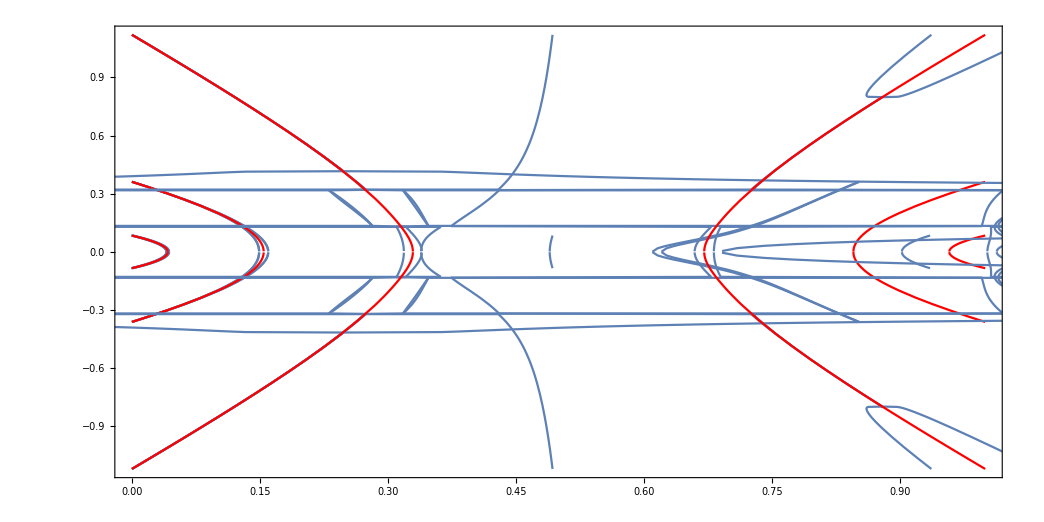

```mathematica
Show[ParametricPlot[{x0+part11A, ys11},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part11A, ys11},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part11B, ys11},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part11B, ys11},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],

ParametricPlot[{x0+part12A, ys12},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part12A, ys12},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part12B, ys12},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part12B, ys12},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦3,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],

ParametricPlot[{x0+part21A, ys21},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part21A, ys21},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part21B, ys21},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part21B, ys21},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦4,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],

ParametricPlot[{x0+part22A, ys22},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part22A, ys22},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part22B, ys22},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part22B, ys22},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦5,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],

ParametricPlot[{x0+part31A, ys31},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part31A, ys31},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part31B, ys31},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part31B, ys31},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦6,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],

ParametricPlot[{x0+part32A, ys32},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part32A, ys32},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part32B, ys32},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part32B, ys32},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
Plot[ys⟦7,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],
AspectRatio-> 1/2]
```

```mathematica
Length[ϵlist⟦5⟧]
```

14

```mathematica
ParametricPlot[{x0+part32A, ys32},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part32A, ys32},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0+part32B, ys32},{x0,0,1},PlotRange->{{0,0.2},All},Frame->True,MaxRecursion->5],
ParametricPlot[{x0-  part32B, ys32},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5],
```

```mathematica
ϵlist⟦5,11,1⟧
```

x0==0.643587

Tratamento cirúrgico:
Estamos utilizando somente os ranges estabelecidos para cada curva na sua plotagem, abaixo temos uma comparação do cenário cirúrgico com o cenário mais aberto (0 a 1 para todas as soluções).

```mathematica
pplots3={};
Table[
ysn = ys⟦7,1,2⟧/.{μ-> 3.8284,x-> x0};
scope = ϵlist⟦5,j⟧;
Which[j ==ranges3⟦1⟧,d=0;u=ϵlist⟦5,j,1,2⟧,
j>ranges3⟦1⟧ And j<ranges3⟦-1⟧, d= ϵlist⟦5,j,1,1⟧;u = ϵlist⟦5,j,1,5⟧,
j == ranges3⟦-1⟧, d=ϵlist⟦5,j,1,2⟧; u=1];
part1 = ϵlist⟦5,j,2,1,2⟧;
part2 = ϵlist⟦5,j,2,2,2⟧;
AppendTo[pplots3,ParametricPlot[{x0+part1, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots3,ParametricPlot[{x0-part1, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots3,ParametricPlot[{x0+part2, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots3,ParametricPlot[{x0-part2, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]],
{j,ranges3}];
```

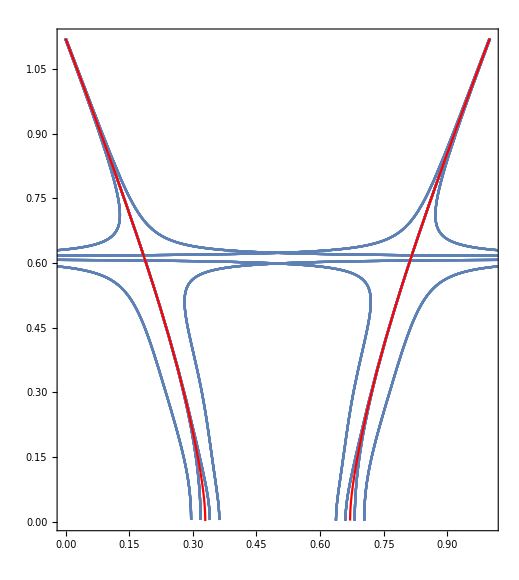

```mathematica
Show[pplots3,Plot[ys⟦7,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red]]
```

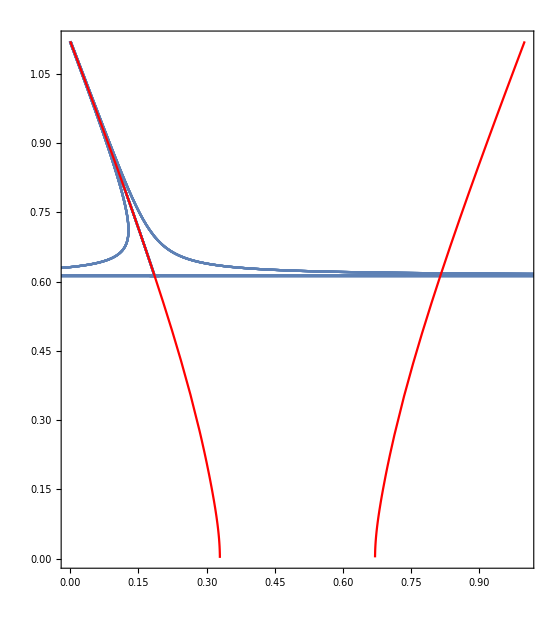

```mathematica
Show[pplots3,Plot[ys⟦7,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red]]
```

```mathematica
pplots={};
Table[
i= n-1;
Table[
ysn = ys⟦n,1,2⟧/.{μ-> 3.8284,x-> x0};
scope = ϵlist⟦i,j⟧;
Which[j ==ranges⟦i,1⟧,d=0;u=ϵlist⟦i,j,1,2⟧,
j>ranges⟦i,1⟧ And j<ranges⟦i,-1⟧, d= ϵlist⟦i,j,1,1⟧;u = ϵlist⟦i,j,1,5⟧,
j == ranges⟦i,-1⟧, d=ϵlist⟦i,j,1,2⟧; u=1];
part1 = ϵlist⟦i,j,2,1,2⟧;
part2 = ϵlist⟦i,j,2,2,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part1, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part1, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0+part2, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part2, ysn},{x0,d,u},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]],
{j,ranges⟦i⟧}],
{n,{2,3,4,5,6,7}}];
```

Part::partd: Part specification ranges⟦1⟧ is longer than depth of object.

Table::iterb: Iterator {j,ranges⟦1⟧} does not have appropriate bounds.

Part::partd: Part specification ranges⟦2⟧ is longer than depth of object.

Table::iterb: Iterator {j,ranges⟦2⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Part::partd: Part specification ranges⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

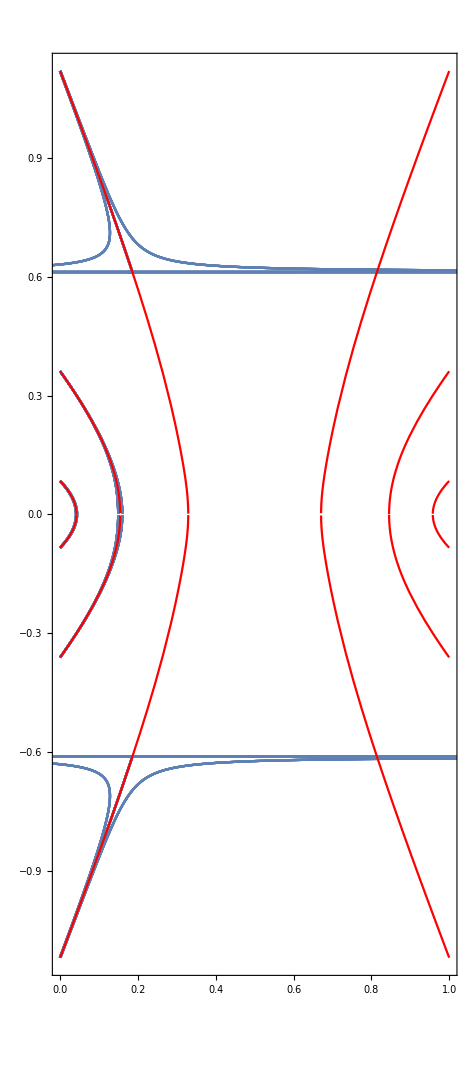

```mathematica
Show[pplots,Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦3,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦4,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦5,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦6,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦7,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red]]
```

```mathematica
ϵlist⟦6,8⟧
```

0.5<x0<0.630601&&(ϵ==-1.57866×10^46 √((1.01359×10^68-1.78866×10^69 x0+1.36277×10^70 x0^2-5.8512×10^70 x0^3+1.54781×10^71 x0^4-2.58262×10^71 x0^5+2.65475×10^71 x0^6-1.5376×10^71 x0^7+3.84401×10^70 x0^8)/((-1.+2. x0)^4 (4.15074×10^83-8.2381×10^84 x0+6.89901×10^85 x0^2-3.19502×10^86 x0^3+8.9594×10^86 x0^4-1.55877×10^87 x0^5+1.64517×10^87 x0^6-9.64779×10^86 x0^7+2.41195×10^86 x0^8)^2))-(5.02453×10^64 (3.18418×10^15-2.81411×10^16 x0+9.03671×10^16 x0^2-1.24452×10^17 x0^3+6.2226×10^16 x0^4))/((-1.+2. x0)^2 (4.15074×10^83-8.2381×10^84 x0+6.89901×10^85 x0^2-3.19502×10^86 x0^3+8.9594×10^86 x0^4-1.55877×10^87 x0^5+1.64517×10^87 x0^6-9.64779×10^86 x0^7+2.41195×10^86 x0^8))||ϵ==1.57866×10^46 √((1.01359×10^68-1.78866×10^69 x0+1.36277×10^70 x0^2-5.8512×10^70 x0^3+1.54781×10^71 x0^4-2.58262×10^71 x0^5+2.65475×10^71 x0^6-1.5376×10^71 x0^7+3.84401×10^70 x0^8)/((-1.+2. x0)^4 (4.15074×10^83-8.2381×10^84 x0+6.89901×10^85 x0^2-3.19502×10^86 x0^3+8.9594×10^86 x0^4-1.55877×10^87 x0^5+1.64517×10^87 x0^6-9.64779×10^86 x0^7+2.41195×10^86 x0^8)^2))+(5.02453×10^64 (3.18418×10^15-2.81411×10^16 x0+9.03671×10^16 x0^2-1.24452×10^17 x0^3+6.2226×10^16 x0^4))/((-1.+2. x0)^2 (4.15074×10^83-8.2381×10^84 x0+6.89901×10^85 x0^2-3.19502×10^86 x0^3+8.9594×10^86 x0^4-1.55877×10^87 x0^5+1.64517×10^87 x0^6-9.64779×10^86 x0^7+2.41195×10^86 x0^8)))

```mathematica
ranges = {{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,5,6,8,9,10},{1,3,5,7,8,10,12,14},{1,3,5,7,8,10,12,14}}
```

{{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,5,6,8,9,10},{1,3,5,7,8,10,12,14},{1,3,5,7,8,10,12,14}}

```mathematica
pplots={};
Table[
i= n-1;
Table[
ysn = ys⟦n,1,2⟧/.{μ-> 3.8284,x-> x0};
scope = ϵlist⟦i,j⟧;
Which[j ==ranges⟦i,1⟧,d=0;u=ϵlist⟦i,j,1,2⟧,
j>ranges⟦i,1⟧ && j<ranges⟦i,-1⟧, d= ϵlist⟦i,j,1,1⟧;u = ϵlist⟦i,j,1,5⟧,
j == ranges⟦i,-1⟧, d=ϵlist⟦i,j,1,2⟧; u=1];
part1 = ϵlist⟦i,j,2,1,2⟧;
part2 = ϵlist⟦i,j,2,2,2⟧;
AppendTo[pplots,ParametricPlot[{x0+part1, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part1, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0+part2, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]];
AppendTo[pplots,ParametricPlot[{x0-part2, ysn},{x0,0,1},PlotRange->{{0,1},All},Frame->True,MaxRecursion->5]],
{j,ranges⟦i⟧}],
{n,{2,3,4,5,6,7}}];
```

Part::partw: Part 5 of x0==0.630601 does not exist.

Part::partw: Part 5 of x0>0.814293 does not exist.

Part::partw: Part 12 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {j,{{1,2,3,4,5,6},{1,2,3,4,5,6},{1,2,3,5,6,8,9,10},{1,3,5,7,8,10,12,14},{1,3,5,7,8,10,12,14}}⟦6⟧} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

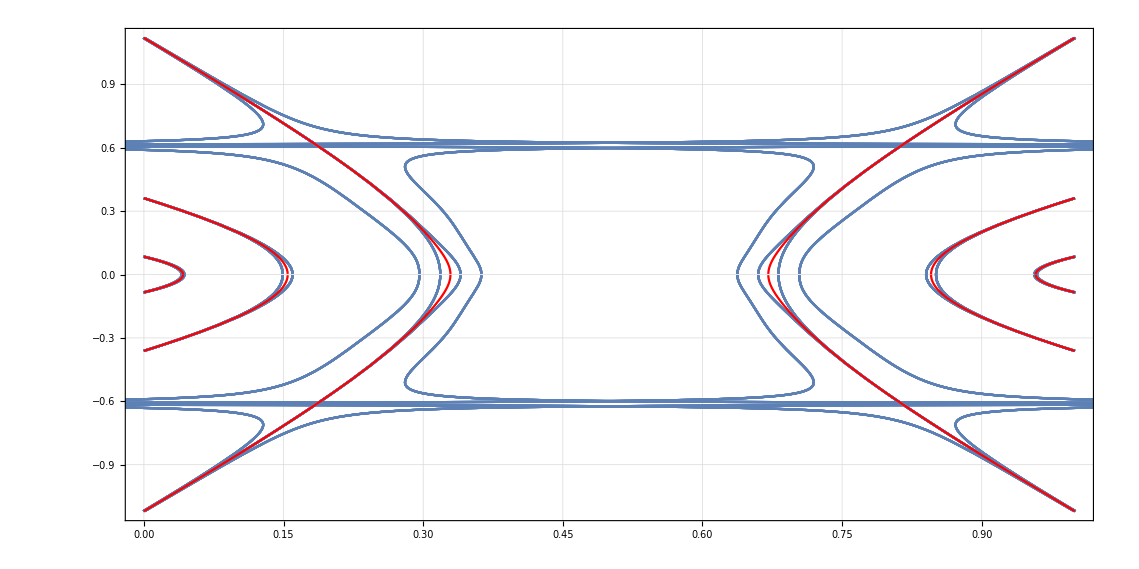

```mathematica
Show[pplots,Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1},GridLines->Automatic,PlotStyle->Red],Plot[ys⟦3,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦4,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦5,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦6,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],Plot[ys⟦7,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2,GridLines->Automatic]
```

```mathematica
plane=-Graphics-;
```

```mathematica
x1=0.328;
y1 = 0.05;
map3[x1,y1,3.8284]
Show[plane,ListPlot[N[{{"0.6756","0.05207"},{"0.6756","-0.02877"},{"0.6676","0.004237"},{"0.6713","0.03805"},{"0.6697","-0.05001"},{"0.6769","0.01245"},{"0.687","-0.1374"},{"0.6906","0.1653"}}]]]
```

1.07858-0.00609346 ⅈ

-Graphics-

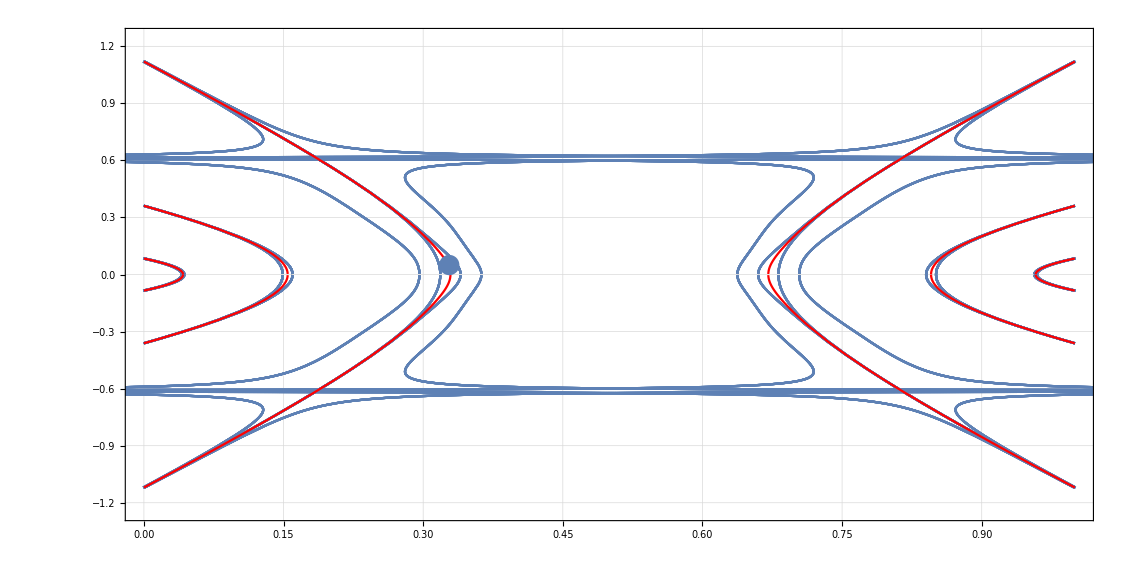

```mathematica
N[{{"0.6756","0.05207"},{"0.6756","-0.02877"},{"0.6676","0.004237"},{"0.6713","0.03805"},{"0.6697","-0.05001"},{"0.6769","0.01245"},{"0.687","-0.1374"},{"0.6906","0.1653"}}]
```

{{0.6756,0.05207},{0.6756,-0.02877},{0.6676,0.004237},{0.6713,0.03805},{0.6697,-0.05001},{0.6769,0.01245},{0.687,-0.1374},{0.6906,0.1653}}